N4m=

16.8488

N4s=

6.10024

N3m=

64.0848

N3s=

10.5158

N2m=

87.6916

N2s=

12.0582

N1m=

53.9937

N1s=

10.8619

N0m=

12.3886

N0s=

5.54414

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

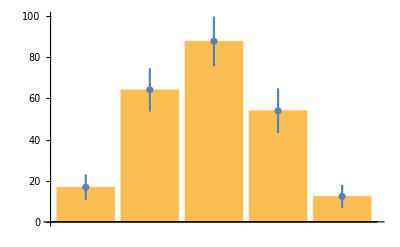

```mathematica
t1=Table[fg=0.52;
p=0.8;
q=0.7;
n=235;
t0=Table[
ng=0;nr=0;
Table[
x=RandomReal[];If[x≤fg,If[RandomReal[]≤p,ng++],If[RandomReal[]≤q,nr++]],
{4}];
{ng,nr},
{n}];
n0g0r=Count[t0,{0,0}];
n1g0r=Count[t0,{1,0}];
n2g0r=Count[t0,{2,0}];
n3g0r=Count[t0,{3,0}];
n4g0r=Count[t0,{4,0}];
n0g1r=Count[t0,{0,1}];
n1g1r=Count[t0,{1,1}];
n2g1r=Count[t0,{2,1}];
n3g1r=Count[t0,{3,1}];
n0g2r=Count[t0,{0,2}];
n1g2r=Count[t0,{1,2}];
n2g2r=Count[t0,{2,2}];
n0g3r=Count[t0,{0,3}];
n1g3r=Count[t0,{1,3}];
n0g4r=Count[t0,{0,4}];
funs={
N4*p^4,
4*N4*p^3*(1-p)+N3*p^3*(1-q),
6*N4*p^2*(1-p)^2+3*N3*p^2*(1-p)*(1-q)+N2*p^2*(1-q)^2,
4*N4*p*(1-p)^3+N1*p*(1-q)^3+2*N2*p*(1-p)*(1-q)^2+3*N3*p*(1-p)^2*(1-q),
N3*p^3*q,
N1*p*q^3,
N2*p^2*q^2,
2*N2*p^2*q*(1-q)+3*N3*p^2*(1-p)*q,
2*N2*p*(1-p)*q^2+3*N1*p*q^2*(1-q),
4*N2*p*(1-p)*q*(1-q)+3*N3*p*(1-p)^2*q+3*N1*p*q*(1-q)^2,
N0*q^4,
4*N0*q^3*(1-q)+N1*(1-p)*q^3,
6*N0*q^2*(1-q)^2+3*N1*(1-p)*q^2*(1-q)+N2*(1-p)^2*q^2,
4*N0*q*(1-q)^3+N3*(1-p)^3*q+2*N2*(1-p)^2*q*(1-q)+3*N1*(1-p)*q*(1-q)^2};

data1 = {n4g0r,n3g0r,n2g0r,n1g0r,n3g1r,n1g3r,n2g2r,n2g1r,n1g2r,n1g1r,n0g4r,n0g3r,n0g2r,n0g1r};

test=Plus@@((funs-data1)^2);
list1=NMinimize[test,{N4,N3,N2,N1,N0}];
list2=list1⟦2⟧;
list3=Values[<|list2|>],{1000}];
N4sim=t1⟦All,1⟧;
N3sim=t1⟦All,2⟧;
N2sim=t1⟦All,3⟧;
N1sim=t1⟦All,4⟧;
N0sim=t1⟦All,5⟧;
Print["N4m="];N4m=Mean[N4sim]
Print["N4s="];N4s=StandardDeviation[N4sim]
Print["N3m="];N3m=Mean[N3sim]
Print["N3s="];N3s=StandardDeviation[N3sim]
Print["N2m="];N2m=Mean[N2sim]
Print["N2s="];N2s=StandardDeviation[N2sim]
Print["N1m="];N1m=Mean[N1sim]
Print["N1s="];N1s=StandardDeviation[N1sim]
Print["N0m="];N0m=Mean[N0sim]
Print["N0s="];N0s=StandardDeviation[N0sim]

Needs["ErrorBarPlots`"]
Show[{BarChart[{N4m,N3m,N2m,N1m,N0m}],
ErrorListPlot[{{N4m,N4s},{N3m,N3s},{N2m,N2s},{N1m,N1s},{N0m,N0s}}]}]
```